## RDKit

```mathematica
session=ResourceFunction["StartPythonSession"][{"rdkit"}]
ExternalEvaluate[session,"from rdkit.Chem import MolFromSmiles, Descriptors"]
features=ExternalFunction[session,"def features(smiles):
      m = MolFromSmiles(smiles)
      vals = Descriptors.CalcMolDescriptors(m)
      return vals"]
```

ExternalSessionObject[…]

ExternalFunction[…]

## External (Test) Data

```mathematica
testdata = Import["/Users/emmaphan/Documents/Comp Chem/Cl Transporter/data/ExternalTest.sdf","Metadata"];
smilestestdata=Lookup["SMILES"]@testdata;
descriptortest = Values/@ features  /@smilestestdata
outputstest = Lookup["Activity"]@testdata
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Length[outputstest]
```

175

```mathematica
Length [descriptortest[[1]]]
```

217

## Training Set 1

```mathematica
trainingset1=Import["/Users/emmaphan/Documents/Comp Chem/Cl Transporter/data/training/ChlorideTransporters-TrainingSet-1.sdf", "Metadata"];
smilestraining1=Lookup["SMILES"]@trainingset1;
Length[smilestraining1]
descriptortraining1=Values/@ features  /@ smilestraining1
Length [descriptortraining1[[1]]]
outputtraining1 = Lookup["Activity"]@trainingset1;
Length[outputtraining1]
```

123

217

123

```mathematica
model1 = Classify[ descriptortraining1-> outputtraining1,FeatureTypes->"NumericalVector",Method->"RandomForest"]
```

ClassifierFunction[…]

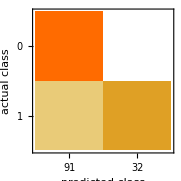
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 123
Accuracy | (82.13.5) %
Accuracy baseline | (56.4.) %
Geometric mean of probabilities | 0.585 ± 0.01
Mean cross entropy | 0.536 ± 0.017
Single evaluation time | 3.76 ms/example
Batch evaluation speed | 970. examples/s
-Graphics- |

```mathematica
ClassifierMeasurements[model1,descriptortraining1->outputtraining1]
```

```mathematica
(*Test on model 1*)
```

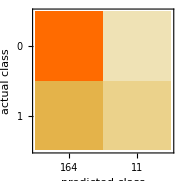
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (83.42.8) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.607 ± 0.0073
Mean cross entropy | 0.5 ± 0.012
Single evaluation time | 3.88 ms/example
Batch evaluation speed | 1.1 examples/ms
-Graphics- |

```mathematica
test1=ClassifierMeasurements[model1, descriptortest-> outputstest ]
```

## Training Set 2

ClassifierFunction[…]

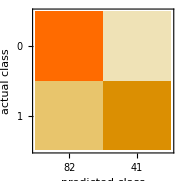
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 123
Accuracy | (86.23.1) %
Accuracy baseline | (56.4.) %
Geometric mean of probabilities | 0.602 ± 0.0084
Mean cross entropy | 0.508 ± 0.014
Single evaluation time | 3.99 ms/example
Batch evaluation speed | 884. examples/s
-Graphics- |

```mathematica
trainingset2=Import["/Users/emmaphan/Documents/Comp Chem/Cl Transporter/Training/ChlorideTransporters-TrainingSet-2.sdf", "Metadata"];
smilestraining2=Lookup["SMILES"]@trainingset2;
descriptortraining2=Values/@ features  /@ smilestraining2;
outputtraining2 = Lookup["Activity"]@trainingset2;

model2 = Classify[ descriptortraining2-> outputtraining2,FeatureTypes->"NumericalVector",Method->"RandomForest"]

ClassifierMeasurements[model2,descriptortraining2->outputtraining2]
```

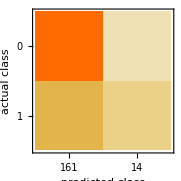
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (84.02.8) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.605 ± 0.0074
Mean cross entropy | 0.502 ± 0.012
Single evaluation time | 9. ms/example
Batch evaluation speed | 952. examples/s
-Graphics- |

```mathematica
test2=ClassifierMeasurements[model2, descriptortest-> outputstest ]
```

## Training Set 3

ClassifierFunction[…]

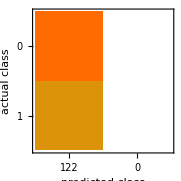
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (56.5.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.521 ± 0.0053
Mean cross entropy | 0.651 ± 0.01
Single evaluation time | 3.77 ms/example
Batch evaluation speed | 1.07 examples/ms
-Graphics- |

```mathematica
trainingset3=Import["/Users/emmaphan/Documents/Comp Chem/Cl Transporter/Training/ChlorideTransporters-TrainingSet-3.sdf", "Metadata"];
smilestraining3=Lookup["SMILES"]@trainingset3;
descriptortraining3=Values/@ features  /@ smilestraining3;
outputtraining3 = Lookup["Activity"]@trainingset3;

model3 = Classify[ descriptortraining3-> outputtraining3,FeatureTypes->"NumericalVector",Method->"RandomForest"]

ClassifierMeasurements[model3,descriptortraining3->outputtraining3]
```

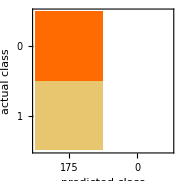
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (82.92.9) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.547 ± 0.0039
Mean cross entropy | 0.604 ± 0.0071
Single evaluation time | 3.61 ms/example
Batch evaluation speed | 1.1 examples/ms
-Graphics- |

```mathematica
test3=ClassifierMeasurements[model3, descriptortest-> outputstest ]
```

## Training Set 4

ClassifierFunction[…]

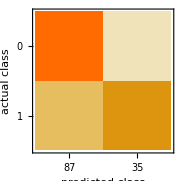
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (82.83.4) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.585 ± 0.0082
Mean cross entropy | 0.536 ± 0.014
Single evaluation time | 3.64 ms/example
Batch evaluation speed | 1.12 examples/ms
-Graphics- |

```mathematica
trainingset4=Import["/Users/emmaphan/Documents/Comp Chem/Cl Transporter/Training/ChlorideTransporters-TrainingSet-3.sdf", "Metadata"];
smilestraining4=Lookup["SMILES"]@trainingset4;
descriptortraining4=Values/@ features  /@ smilestraining4;
outputtraining4 = Lookup["Activity"]@trainingset4;

model4 = Classify[ descriptortraining4-> outputtraining4,FeatureTypes->"NumericalVector",Method->"RandomForest"]

ClassifierMeasurements[model4,descriptortraining4->outputtraining4]
```

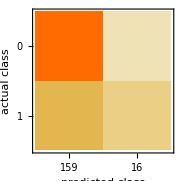
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (86.32.6) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.595 ± 0.007
Mean cross entropy | 0.519 ± 0.012
Single evaluation time | 3.75 ms/example
Batch evaluation speed | 1.07 examples/ms
-Graphics- |

```mathematica
test4=ClassifierMeasurements[model4, descriptortest-> outputstest ]
```

## Training Set 5

ClassifierFunction[…]

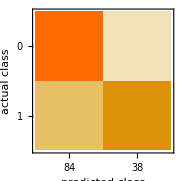
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (83.63.4) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.545 ± 0.0045
Mean cross entropy | 0.607 ± 0.0082
Single evaluation time | 3.77 ms/example
Batch evaluation speed | 3.2 examples/ms
-Graphics- |

```mathematica
trainingset5=Import["/Users/emmaphan/Documents/Comp Chem/Cl Transporter/Training/ChlorideTransporters-TrainingSet-5.sdf", "Metadata"];
smilestraining5=Lookup["SMILES"]@trainingset5;
descriptortraining5=Values/@ features  /@ smilestraining5;
outputtraining5 = Lookup["Activity"]@trainingset5;

model5 = Classify[ descriptortraining5-> outputtraining5,FeatureTypes->"NumericalVector",Method->"RandomForest"]

ClassifierMeasurements[model5,descriptortraining5->outputtraining5]
```

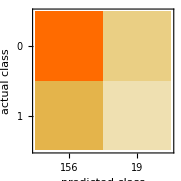
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (81.13.0) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.55 ± 0.0043
Mean cross entropy | 0.599 ± 0.0078
Single evaluation time | 3.65 ms/example
Batch evaluation speed | 1.22 examples/ms
-Graphics- |

```mathematica
test5=ClassifierMeasurements[model5, descriptortest-> outputstest ]
```

## Training Set 6

ClassifierFunction[…]

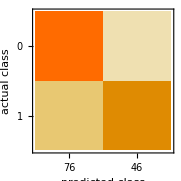
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (86.93.1) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.647 ± 0.014
Mean cross entropy | 0.436 ± 0.022
Single evaluation time | 3.92 ms/example
Batch evaluation speed | 961. examples/s
-Graphics- |

```mathematica
trainingset6=Import["/Users/emmaphan/Documents/Comp Chem/Cl Transporter/Training/ChlorideTransporters-TrainingSet-6.sdf", "Metadata"];
smilestraining6=Lookup["SMILES"]@trainingset6;
descriptortraining6=Values/@ features  /@ smilestraining6;
outputtraining6 = Lookup["Activity"]@trainingset6;

model6 = Classify[ descriptortraining6-> outputtraining6,FeatureTypes->"NumericalVector",Method->"RandomForest"]

ClassifierMeasurements[model6,descriptortraining6->outputtraining6]
```

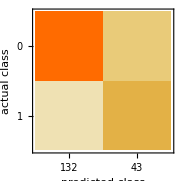
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (85.72.7) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.642 ± 0.011
Mean cross entropy | 0.443 ± 0.018
Single evaluation time | 3.76 ms/example
Batch evaluation speed | 1.1 examples/ms
-Graphics- |

```mathematica
test6=ClassifierMeasurements[model6, descriptortest-> outputstest ]
```

## Training Set 7

ClassifierFunction[…]

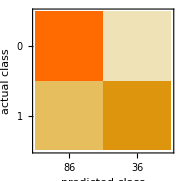
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (82.03.5) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.576 ± 0.0079
Mean cross entropy | 0.551 ± 0.014
Single evaluation time | 4.87 ms/example
Batch evaluation speed | 2.34 examples/ms
-Graphics- |

```mathematica
trainingset7=Import["/Users/emmaphan/Documents/Comp Chem/Cl Transporter/Training/ChlorideTransporters-TrainingSet-7.sdf", "Metadata"];
smilestraining7=Lookup["SMILES"]@trainingset7;
descriptortraining7=Values/@ features  /@ smilestraining7;
outputtraining7 = Lookup["Activity"]@trainingset7;

model7 = Classify[ descriptortraining7-> outputtraining7,FeatureTypes->"NumericalVector",Method->"RandomForest"]

ClassifierMeasurements[model7,descriptortraining7->outputtraining7]
```

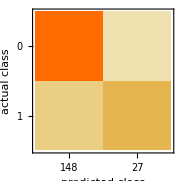
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (88.02.5) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.595 ± 0.0063
Mean cross entropy | 0.518 ± 0.011
Single evaluation time | 3.85 ms/example
Batch evaluation speed | 1.15 examples/ms
-Graphics- |

```mathematica
test7=ClassifierMeasurements[model7, descriptortest-> outputstest ]
```

## Training Set 8

ClassifierFunction[…]

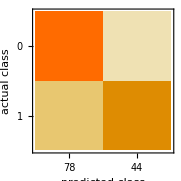
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (86.93.1) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.62 ± 0.013
Mean cross entropy | 0.478 ± 0.021
Single evaluation time | 3.63 ms/example
Batch evaluation speed | 1.08 examples/ms
-Graphics- |

```mathematica
trainingset8=Import["/Users/emmaphan/Documents/Comp Chem/Cl Transporter/Training/ChlorideTransporters-TrainingSet-8.sdf", "Metadata"];
smilestraining8=Lookup["SMILES"]@trainingset8;
descriptortraining8=Values/@ features  /@ smilestraining8;
outputtraining8 = Lookup["Activity"]@trainingset8;

model8 = Classify[ descriptortraining8-> outputtraining8,FeatureTypes->"NumericalVector",Method->"RandomForest"]

ClassifierMeasurements[model8,descriptortraining8->outputtraining8]
```

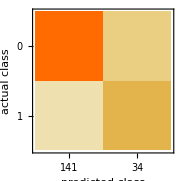
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (87.42.5) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.63 ± 0.0095
Mean cross entropy | 0.462 ± 0.015
Single evaluation time | 3.72 ms/example
Batch evaluation speed | 1.07 examples/ms
-Graphics- |

```mathematica
test8=ClassifierMeasurements[model8, descriptortest-> outputstest ]
```

## Training Set 9

ClassifierFunction[…]

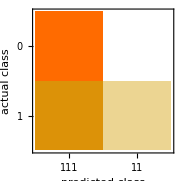
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (65.4.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.537 ± 0.0054
Mean cross entropy | 0.622 ± 0.01
Single evaluation time | 3.69 ms/example
Batch evaluation speed | 1.11 examples/ms
-Graphics- |

```mathematica
trainingset9=Import["/Users/emmaphan/Documents/Comp Chem/Cl Transporter/Training/ChlorideTransporters-TrainingSet-9.sdf", "Metadata"];
smilestraining9=Lookup["SMILES"]@trainingset9;
descriptortraining9=Values/@ features  /@ smilestraining9;
outputtraining9 = Lookup["Activity"]@trainingset9;

model9 = Classify[ descriptortraining9-> outputtraining9,FeatureTypes->"NumericalVector",Method->"RandomForest"]

ClassifierMeasurements[model9,descriptortraining9->outputtraining9]
```

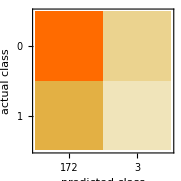
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (82.32.9) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.558 ± 0.0039
Mean cross entropy | 0.584 ± 0.007
Single evaluation time | 3.78 ms/example
Batch evaluation speed | 1.07 examples/ms
-Graphics- |

```mathematica
test9=ClassifierMeasurements[model9, descriptortest-> outputstest ]
```

## Training Set 10

ClassifierFunction[…]

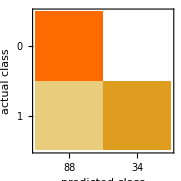
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (83.63.4) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.583 ± 0.0095
Mean cross entropy | 0.539 ± 0.016
Single evaluation time | 3.74 ms/example
Batch evaluation speed | 934. examples/s
-Graphics- |

```mathematica
trainingset10=Import["/Users/emmaphan/Documents/Comp Chem/Cl Transporter/Training/ChlorideTransporters-TrainingSet-10.sdf", "Metadata"];
smilestraining10=Lookup["SMILES"]@trainingset10;
descriptortraining10=Values/@ features  /@ smilestraining10;
outputtraining10 = Lookup["Activity"]@trainingset10;

model10 = Classify[ descriptortraining10-> outputtraining10,FeatureTypes->"NumericalVector",Method->"RandomForest"]

ClassifierMeasurements[model10,descriptortraining10->outputtraining10]
```

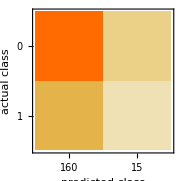
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (82.32.9) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.593 ± 0.0074
Mean cross entropy | 0.522 ± 0.012
Single evaluation time | 3.75 ms/example
Batch evaluation speed | 1.06 examples/ms
-Graphics- |

```mathematica
test10=ClassifierMeasurements[model10, descriptortest-> outputstest ]
```

## Training Set 11

ClassifierFunction[…]

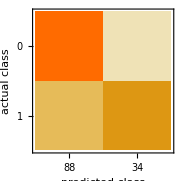
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (80.4.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.567 ± 0.0077
Mean cross entropy | 0.567 ± 0.014
Single evaluation time | 4.26 ms/example
Batch evaluation speed | 1.04 examples/ms
-Graphics- |

```mathematica
trainingset11=Import["/Users/emmaphan/Documents/Comp Chem/Cl Transporter/Training/ChlorideTransporters-TrainingSet-11.sdf", "Metadata"];
smilestraining11=Lookup["SMILES"]@trainingset11;
descriptortraining11=Values/@ features  /@ smilestraining11;
outputtraining11 = Lookup["Activity"]@trainingset11;

model11 = Classify[ descriptortraining11-> outputtraining11,FeatureTypes->"NumericalVector",Method->"RandomForest"]

ClassifierMeasurements[model11,descriptortraining11->outputtraining11]
```

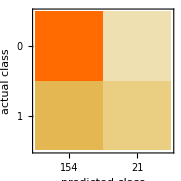
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (85.72.7) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.589 ± 0.0059
Mean cross entropy | 0.529 ± 0.01
Single evaluation time | 3.85 ms/example
Batch evaluation speed | 1.06 examples/ms
-Graphics- |

```mathematica
test11=ClassifierMeasurements[model11, descriptortest-> outputstest ]
```

## Training Set 12

ClassifierFunction[…]

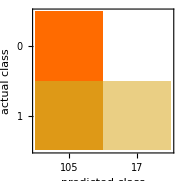
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (70.4.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.557 ± 0.0069
Mean cross entropy | 0.585 ± 0.012
Single evaluation time | 22.5 ms/example
Batch evaluation speed | 934. examples/s
-Graphics- |

```mathematica
trainingset12=Import["/Users/emmaphan/Documents/Comp Chem/Cl Transporter/Training/ChlorideTransporters-TrainingSet-12.sdf", "Metadata"];
smilestraining12=Lookup["SMILES"]@trainingset12;
descriptortraining12=Values/@ features  /@ smilestraining12;
outputtraining12 = Lookup["Activity"]@trainingset12;

model12 = Classify[ descriptortraining12-> outputtraining12,FeatureTypes->"NumericalVector",Method->"RandomForest"]

ClassifierMeasurements[model12,descriptortraining12->outputtraining12]
```

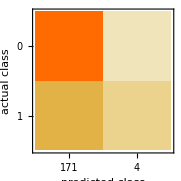
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (84.02.8) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.578 ± 0.0056
Mean cross entropy | 0.549 ± 0.0098
Single evaluation time | 3.69 ms/example
Batch evaluation speed | 1.07 examples/ms
-Graphics- |

```mathematica
test12=ClassifierMeasurements[model12, descriptortest-> outputstest ]
```

## Training Set 13

ClassifierFunction[…]

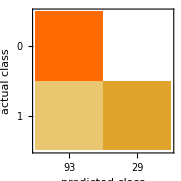
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (80.4.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.56 ± 0.0074
Mean cross entropy | 0.579 ± 0.013
Single evaluation time | 27.8 ms/example
Batch evaluation speed | 591. examples/s
-Graphics- |

```mathematica
trainingset13=Import["/Users/emmaphan/Documents/Comp Chem/Cl Transporter/Training/ChlorideTransporters-TrainingSet-13.sdf", "Metadata"];
smilestraining13=Lookup["SMILES"]@trainingset13;
descriptortraining13=Values/@ features  /@ smilestraining13;
outputtraining13 = Lookup["Activity"]@trainingset13;

model13 = Classify[ descriptortraining13-> outputtraining13,FeatureTypes->"NumericalVector",Method->"RandomForest"]

ClassifierMeasurements[model13,descriptortraining13->outputtraining13]
```

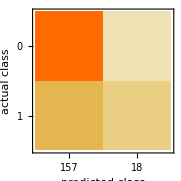
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (85.12.7) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.579 ± 0.0054
Mean cross entropy | 0.547 ± 0.0094
Single evaluation time | 3.83 ms/example
Batch evaluation speed | 980. examples/s
-Graphics- |

```mathematica
test13=ClassifierMeasurements[model13, descriptortest-> outputstest ]
```

## Training Set 14

ClassifierFunction[…]

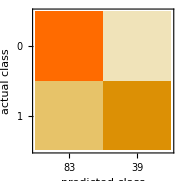
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (86.13.1) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.587 ± 0.0086
Mean cross entropy | 0.533 ± 0.015
Single evaluation time | 3.81 ms/example
Batch evaluation speed | 1.12 examples/ms
-Graphics- |

```mathematica
trainingset14=Import["/Users/emmaphan/Documents/Comp Chem/Cl Transporter/Training/ChlorideTransporters-TrainingSet-14.sdf", "Metadata"];
smilestraining14=Lookup["SMILES"]@trainingset14;
descriptortraining14=Values/@ features  /@ smilestraining14;
outputtraining14 = Lookup["Activity"]@trainingset14;

model14 = Classify[ descriptortraining14-> outputtraining14,FeatureTypes->"NumericalVector",Method->"RandomForest"]

ClassifierMeasurements[model14,descriptortraining14->outputtraining14]
```

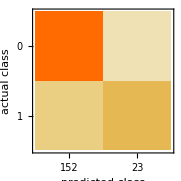
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (88.02.5) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.601 ± 0.0065
Mean cross entropy | 0.509 ± 0.011
Single evaluation time | 3.94 ms/example
Batch evaluation speed | 1.06 examples/ms
-Graphics- |

```mathematica
test14=ClassifierMeasurements[model14, descriptortest-> outputstest ]
```

## Training Set 15

ClassifierFunction[…]

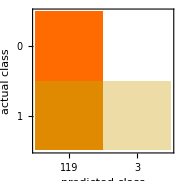
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (58.4.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.528 ± 0.0053
Mean cross entropy | 0.638 ± 0.01
Single evaluation time | 3.74 ms/example
Batch evaluation speed | 970. examples/s
-Graphics- |

```mathematica
trainingset15=Import["/Users/emmaphan/Documents/Comp Chem/Cl Transporter/Training/ChlorideTransporters-TrainingSet-15.sdf", "Metadata"];
smilestraining15=Lookup["SMILES"]@trainingset15;
descriptortraining15=Values/@ features  /@ smilestraining15;
outputtraining15 = Lookup["Activity"]@trainingset15;

model15 = Classify[ descriptortraining15-> outputtraining15,FeatureTypes->"NumericalVector",Method->"RandomForest"]

ClassifierMeasurements[model15,descriptortraining15->outputtraining15]
```

```mathematica
test15=ClassifierMeasurements[model15, descriptortest-> outputstest ]
```

Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (82.92.9) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.551 ± 0.0037
Mean cross entropy | 0.596 ± 0.0067
Single evaluation time | 3.72 ms/example
Batch evaluation speed | 1.09 examples/ms
-Graphics- |

## Training Set 16

```mathematica
trainingset16=Import["/Users/emmaphan/Documents/Comp Chem/Cl Transporter/Training/ChlorideTransporters-TrainingSet-16.sdf", "Metadata"];
smilestraining16=Lookup["SMILES"]@trainingset16;
descriptortraining16=Values/@ features  /@ smilestraining16;
outputtraining16 = Lookup["Activity"]@trainingset16;

model16 = Classify[ descriptortraining16-> outputtraining16,FeatureTypes->"NumericalVector",Method->"RandomForest"]

ClassifierMeasurements[model16,descriptortraining16->outputtraining16]
```

ClassifierFunction[…]

Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (56.5.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.512 ± 0.0043
Mean cross entropy | 0.669 ± 0.0083
Single evaluation time | 3.66 ms/example
Batch evaluation speed | 3.26 examples/ms
-Graphics- |

```mathematica
test16=ClassifierMeasurements[model16, descriptortest-> outputstest ]
```

Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (82.92.9) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.535 ± 0.0029
Mean cross entropy | 0.625 ± 0.0053
Single evaluation time | 3.71 ms/example
Batch evaluation speed | 1.22 examples/ms
-Graphics- |

## Training Set 17

ClassifierFunction[…]

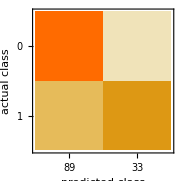
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (81.4.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.566 ± 0.0071
Mean cross entropy | 0.569 ± 0.013
Single evaluation time | 3.67 ms/example
Batch evaluation speed | 2.79 examples/ms
-Graphics- |

```mathematica
trainingset17=Import["/Users/emmaphan/Documents/Comp Chem/Cl Transporter/Training/ChlorideTransporters-TrainingSet-17.sdf", "Metadata"];
smilestraining17=Lookup["SMILES"]@trainingset17;
descriptortraining17=Values/@ features  /@ smilestraining17;
outputtraining17 = Lookup["Activity"]@trainingset17;

model17 = Classify[ descriptortraining17-> outputtraining17,FeatureTypes->"NumericalVector",Method->"RandomForest"]

ClassifierMeasurements[model17,descriptortraining17->outputtraining17]
```

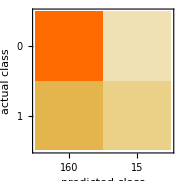
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (84.62.7) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.582 ± 0.0058
Mean cross entropy | 0.541 ± 0.01
Single evaluation time | 3.84 ms/example
Batch evaluation speed | 1.21 examples/ms
-Graphics- |

```mathematica
test17=ClassifierMeasurements[model17, descriptortest-> outputstest ]
```

## Training Set 18

ClassifierFunction[…]

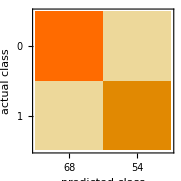
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (88.52.9) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.686 ± 0.015
Mean cross entropy | 0.377 ± 0.021
Single evaluation time | 3.85 ms/example
Batch evaluation speed | 1.08 examples/ms
-Graphics- |

```mathematica
trainingset18=Import["/Users/emmaphan/Documents/Comp Chem/Cl Transporter/Training/ChlorideTransporters-TrainingSet-18.sdf", "Metadata"];
smilestraining18=Lookup["SMILES"]@trainingset18;
descriptortraining18=Values/@ features  /@ smilestraining18;
outputtraining18 = Lookup["Activity"]@trainingset18;

model18 = Classify[ descriptortraining18-> outputtraining18,FeatureTypes->"NumericalVector",Method->"RandomForest"]

ClassifierMeasurements[model18,descriptortraining18->outputtraining18]
```

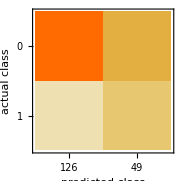
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (81.13.0) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.628 ± 0.015
Mean cross entropy | 0.465 ± 0.024
Single evaluation time | 3.75 ms/example
Batch evaluation speed | 1.08 examples/ms
-Graphics- |

```mathematica
test18=ClassifierMeasurements[model18, descriptortest-> outputstest ]
```

## Training Set 19

ClassifierFunction[…]

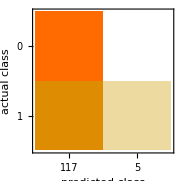
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (60.4.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.544 ± 0.0073
Mean cross entropy | 0.608 ± 0.013
Single evaluation time | 3.72 ms/example
Batch evaluation speed | 1.11 examples/ms
-Graphics- |

```mathematica
trainingset19=Import["/Users/emmaphan/Documents/Comp Chem/Cl Transporter/Training/ChlorideTransporters-TrainingSet-19.sdf", "Metadata"];
smilestraining19=Lookup["SMILES"]@trainingset19;
descriptortraining19=Values/@ features  /@ smilestraining19;
outputtraining19 = Lookup["Activity"]@trainingset19;

model19 = Classify[ descriptortraining19-> outputtraining19,FeatureTypes->"NumericalVector",Method->"RandomForest"]

ClassifierMeasurements[model19,descriptortraining19->outputtraining19]
```

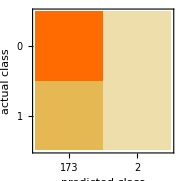
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (82.92.9) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.571 ± 0.0053
Mean cross entropy | 0.56 ± 0.0092
Single evaluation time | 3.75 ms/example
Batch evaluation speed | 1.1 examples/ms
-Graphics- |

```mathematica
test19=ClassifierMeasurements[model19, descriptortest-> outputstest ]
```

## Accuracy

```mathematica
tests={test1,test2,test3,test4,test5,test6,test7,test8,test9,test10,test11,test12,test13,test14,test15, test16,test17,test18,test19};
accuracies=Table[tests[[i]]["Accuracy"],{i,Length[tests]}]
```

{0.834286,0.84,0.828571,0.862857,0.811429,0.857143,0.88,0.874286,0.822857,0.822857,0.857143,0.84,0.851429,0.88,0.828571,0.828571,0.845714,0.811429,0.828571}

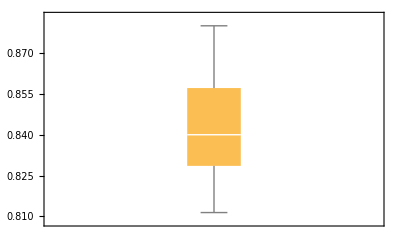

```mathematica
autorfbox=BoxWhiskerChart[accuracies]
```

## CCR = Correct/Total

```mathematica
Length@test1["CorrectlyClassifiedExamples"]
```

146

```mathematica
Length@test1["Examples"]
```

175

```mathematica
Head@test1
```

ClassifierMeasurementsObject

```mathematica
ccr[ex_ClassifierMeasurementsObject]:=Length@ex["CorrectlyClassifiedExamples"]/Length@ex["Examples"]//N
```

```mathematica
BoxWhiskerChart[ccr/@tests]
```

-Graphics-

## Train with hyperparameter in the paper

For RF,the maximum depth was set to 10,and the number of estimators for hyperparameter
optimization was set to 5,10,and 25. The number of estimators is number of trees in forest “TreeNumber”

```mathematica
traininglist={trainingset1,trainingset2,trainingset3,trainingset4,trainingset5,trainingset6,trainingset7,trainingset8,trainingset9,trainingset10,trainingset11,trainingset12,trainingset13,trainingset14,trainingset15,trainingset16,trainingset17,trainingset18,trainingset19};
descriptorlist={descriptortraining1,descriptortraining2,descriptortraining3,descriptortraining4,descriptortraining5,descriptortraining6,descriptortraining7,descriptortraining8,descriptortraining9,descriptortraining10,descriptortraining11,descriptortraining12,descriptortraining13,descriptortraining14,descriptortraining15,descriptortraining16,descriptortraining17,descriptortraining18,descriptortraining19};
outputlist={outputtraining1,outputtraining2,outputtraining3,outputtraining4,outputtraining5,outputtraining6,outputtraining7,outputtraining8,outputtraining9,outputtraining10,outputtraining11,outputtraining12,outputtraining13,outputtraining14,outputtraining15,outputtraining16,outputtraining17,outputtraining18,outputtraining19};
```

```mathematica
rf5 = Classify[ descriptortraining1-> outputtraining1,Method->{"RandomForest","TreeNumber"-> 5}] (*example on one training set*)
```

ClassifierFunction[…]

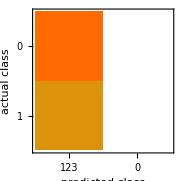
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 123
Accuracy | (56.4.) %
Accuracy baseline | (56.4.) %
Geometric mean of probabilities | 0.525 ± 0.0066
Mean cross entropy | 0.645 ± 0.013
Single evaluation time | 14.9 ms/example
Batch evaluation speed | 546. examples/s
-Graphics- |

```mathematica
ClassifierMeasurements[rf5,descriptortraining1->outputtraining1]
```

```mathematica
(*apply to 19 dataset*)
```

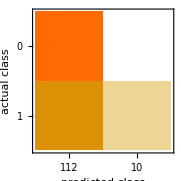
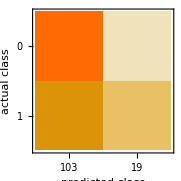
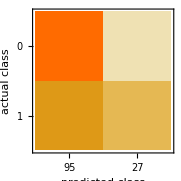
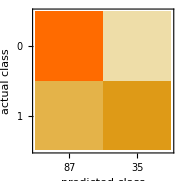
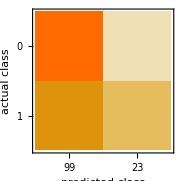
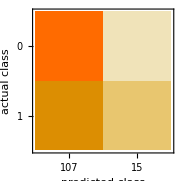
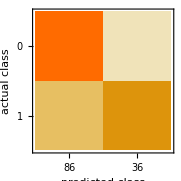
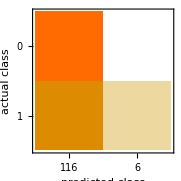
{Classifier Measurements
Classifier method | RandomForest
Number of test examples | 123
Accuracy | (56.4.) %
Accuracy baseline | (56.4.) %
Geometric mean of probabilities | 0.497 ± 0.0036
Mean cross entropy | 0.7 ± 0.0072
Single evaluation time | 2.21 ms/example
Batch evaluation speed | 1.02 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 123
Accuracy | (56.4.) %
Accuracy baseline | (56.4.) %
Geometric mean of probabilities | 0.516 ± 0.0046
Mean cross entropy | 0.662 ± 0.0089
Single evaluation time | 2.1 ms/example
Batch evaluation speed | 1.21 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (64.4.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.532 ± 0.0055
Mean cross entropy | 0.632 ± 0.01
Single evaluation time | 2.09 ms/example
Batch evaluation speed | 1.23 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (56.5.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.512 ± 0.0071
Mean cross entropy | 0.669 ± 0.014
Single evaluation time | 2.37 ms/example
Batch evaluation speed | 1.06 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (56.5.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.518 ± 0.0043
Mean cross entropy | 0.657 ± 0.0083
Single evaluation time | 2.33 ms/example
Batch evaluation speed | 3.52 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (70.4.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.554 ± 0.0074
Mean cross entropy | 0.591 ± 0.013
Single evaluation time | 2.37 ms/example
Batch evaluation speed | 1.03 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (56.5.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.514 ± 0.004
Mean cross entropy | 0.665 ± 0.0077
Single evaluation time | 2.46 ms/example
Batch evaluation speed | 3.74 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (73.4.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.555 ± 0.0084
Mean cross entropy | 0.589 ± 0.015
Single evaluation time | 2.07 ms/example
Batch evaluation speed | 1.21 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (73.4.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.524 ± 0.0047
Mean cross entropy | 0.645 ± 0.009
Single evaluation time | 2.86 ms/example
Batch evaluation speed | 970. examples/s
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (70.4.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.536 ± 0.0068
Mean cross entropy | 0.624 ± 0.013
Single evaluation time | 2.28 ms/example
Batch evaluation speed | 877. examples/s
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (56.5.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.518 ± 0.0053
Mean cross entropy | 0.657 ± 0.01
Single evaluation time | 2.55 ms/example
Batch evaluation speed | 1.07 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (66.4.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.529 ± 0.006
Mean cross entropy | 0.637 ± 0.011
Single evaluation time | 20.6 ms/example
Batch evaluation speed | 1.02 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (56.5.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.524 ± 0.0055
Mean cross entropy | 0.646 ± 0.01
Single evaluation time | 20.3 ms/example
Batch evaluation speed | 1.18 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (83.63.4) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.572 ± 0.012
Mean cross entropy | 0.559 ± 0.02
Single evaluation time | 2.3 ms/example
Batch evaluation speed | 952. examples/s
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (64.4.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.541 ± 0.0075
Mean cross entropy | 0.615 ± 0.014
Single evaluation time | 2.16 ms/example
Batch evaluation speed | 1.02 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (61.4.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.537 ± 0.0066
Mean cross entropy | 0.621 ± 0.012
Single evaluation time | 2.11 ms/example
Batch evaluation speed | 4.14 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (61.4.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.526 ± 0.0051
Mean cross entropy | 0.643 ± 0.0097
Single evaluation time | 2.16 ms/example
Batch evaluation speed | 4.14 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (83.63.4) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.617 ± 0.013
Mean cross entropy | 0.483 ± 0.022
Single evaluation time | 2.26 ms/example
Batch evaluation speed | 1.01 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 122
Accuracy | (70.4.) %
Accuracy baseline | (56.5.) %
Geometric mean of probabilities | 0.558 ± 0.0099
Mean cross entropy | 0.583 ± 0.018
Single evaluation time | 2.21 ms/example
Batch evaluation speed | 1.11 examples/ms
-Graphics- | }

```mathematica
traininglist=MapThread[Thread[#1->#2]&,{descriptorlist,outputlist}]; (*associattio of descriptor and output*)
rf5models = Table[Classify[traininglist[[i]],FeatureTypes->"NumericalVector",Method-> {"RandomForest","TreeNumber"-> 5}], {i,Length[traininglist]}];
rf5cmlist=Table[ClassifierMeasurements[rf5models [[i]],trainSets[[i]]],{i,Length[rf5models ]}]
```

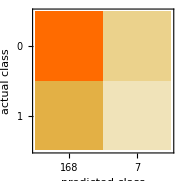
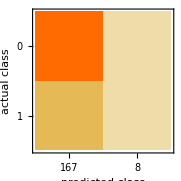
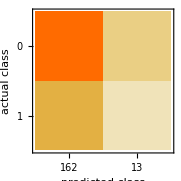
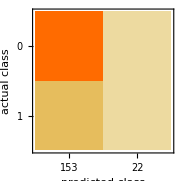
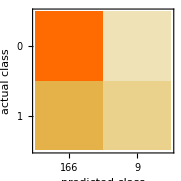
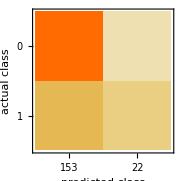
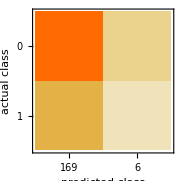
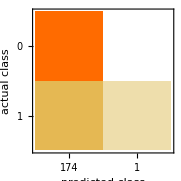
{Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (82.92.9) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.52 ± 0.0023
Mean cross entropy | 0.653 ± 0.0044
Single evaluation time | 3.65 ms/example
Batch evaluation speed | 1.07 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (82.92.9) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.539 ± 0.0033
Mean cross entropy | 0.617 ± 0.0061
Single evaluation time | 2.31 ms/example
Batch evaluation speed | 1.15 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (81.13.0) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.552 ± 0.0047
Mean cross entropy | 0.594 ± 0.0085
Single evaluation time | 2.18 ms/example
Batch evaluation speed | 1.17 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (82.92.9) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.552 ± 0.0048
Mean cross entropy | 0.594 ± 0.0086
Single evaluation time | 2.24 ms/example
Batch evaluation speed | 1.15 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (82.92.9) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.539 ± 0.0036
Mean cross entropy | 0.618 ± 0.0066
Single evaluation time | 2.35 ms/example
Batch evaluation speed | 1.28 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (82.92.9) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.575 ± 0.0052
Mean cross entropy | 0.554 ± 0.0091
Single evaluation time | 2.46 ms/example
Batch evaluation speed | 1.11 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (82.92.9) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.533 ± 0.0026
Mean cross entropy | 0.629 ± 0.0049
Single evaluation time | 2.13 ms/example
Batch evaluation speed | 1.29 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (77.73.2) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.575 ± 0.0061
Mean cross entropy | 0.553 ± 0.011
Single evaluation time | 2.24 ms/example
Batch evaluation speed | 1.18 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (82.92.9) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.544 ± 0.0039
Mean cross entropy | 0.61 ± 0.0072
Single evaluation time | 2.41 ms/example
Batch evaluation speed | 1. examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (77.73.2) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.559 ± 0.0051
Mean cross entropy | 0.581 ± 0.0091
Single evaluation time | 2.22 ms/example
Batch evaluation speed | 1.13 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (82.92.9) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.547 ± 0.0039
Mean cross entropy | 0.603 ± 0.0071
Single evaluation time | 2.18 ms/example
Batch evaluation speed | 1.16 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (83.42.8) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.56 ± 0.0043
Mean cross entropy | 0.579 ± 0.0077
Single evaluation time | 2.25 ms/example
Batch evaluation speed | 1.14 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (82.92.9) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.554 ± 0.0044
Mean cross entropy | 0.59 ± 0.008
Single evaluation time | 2.25 ms/example
Batch evaluation speed | 1.07 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (86.32.6) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.617 ± 0.0089
Mean cross entropy | 0.483 ± 0.014
Single evaluation time | 2.15 ms/example
Batch evaluation speed | 1.17 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (81.72.9) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.565 ± 0.0057
Mean cross entropy | 0.572 ± 0.01
Single evaluation time | 2.29 ms/example
Batch evaluation speed | 1.13 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (83.42.8) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.553 ± 0.0055
Mean cross entropy | 0.592 ± 0.0099
Single evaluation time | 6.54 ms/example
Batch evaluation speed | 1.29 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (80.63.0) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.541 ± 0.0042
Mean cross entropy | 0.614 ± 0.0077
Single evaluation time | 2.17 ms/example
Batch evaluation speed | 1.27 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (78.93.1) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.601 ± 0.011
Mean cross entropy | 0.51 ± 0.018
Single evaluation time | 2.11 ms/example
Batch evaluation speed | 1.14 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (84.02.8) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.597 ± 0.0072
Mean cross entropy | 0.516 ± 0.012
Single evaluation time | 2.17 ms/example
Batch evaluation speed | 1.17 examples/ms
-Graphics- | }

```mathematica
descriptortestlist =ConstantArray[descriptortest,19];
outputstestlist=ConstantArray[outputstest,19]; 
testlist=MapThread[Thread[#1->#2]&,{descriptortestlist,outputstestlist}];
rf5test = Table [ClassifierMeasurements[rf5models[[i]],testlist[[i]]],{i, Length[rf5models]}]
```

```mathematica
rf5accuracy= Table [rf5test[[i]]["Accuracy"], {i,Length[rf5test]}]
```

{0.828571,0.828571,0.811429,0.828571,0.828571,0.828571,0.828571,0.777143,0.828571,0.777143,0.828571,0.834286,0.828571,0.862857,0.817143,0.834286,0.805714,0.788571,0.84}

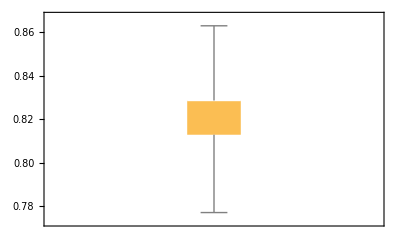

```mathematica
rf5box=BoxWhiskerChart[rf5accuracy]
```

```mathematica
autorfbox
```

-Graphics-

```mathematica
net=NetChain[
{LinearLayer[100],Ramp,DropoutLayer[0.2],50,Ramp,LinearLayer[],LogisticSigmoid},
"Input"->217,
"Output"->NetDecoder["Boolean"]]
```

NetChain[…]

```mathematica
?NetChain
```

```mathematica
?NetTrain
```

```mathematica
descriptortraining19[[71]]
```

{11.5345,11.5345,0.279144,-5.24878,0.494773,11.2632,323.136,313.056,322.977,98,0,Indeterminate,Indeterminate,Indeterminate,Indeterminate,1.05263,1.68421,2.21053,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,2.37735,2.68459,665.075,14.0436,9.6324,11.509,8.89287,5.29365,8.67651,3.86862,7.16231,2.59075,4.68387,1.73641,3.45243,-1.88156,16669.9,13.5478,5.00965,2.92925,111.026,0.,0.,0.,0.,0.,110.837,0.,0.,0.,0.,0.,0.,0.,0.,16.8541,24.2112,0.,0.,0.,0.,0.,58.6453,0.,11.1269,4.35119,5.68739,0.,0.,27.2873,3.73949,10.1143,0.,48.5309,0.,11.1269,0.,100.67,19.0959,22.0452,0.,10.0386,11.1269,6.06637,12.1327,30.3318,0.,0.,0.,30.0286,-5.24878,10.0104,10.6873,0.592816,0.,12.1589,0.,0.,0.,0.,19,2,6,0,0,0,0,2,0,2,0,0,3,2,7,0,3,0,0,0,0,0,3.57209,2,0.8228,69.0445,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Length[descriptortraining1[[1]]]
```

217

```mathematica
NetTrain[net,descriptortraining19-> outputtraining19]
```

NetTrain::invindim2: Data provided to port "Input" should be a non-empty list of length-217 vectors, but element #71 was a list of non-numeric values.

$Failed